```mathematica
Needs["ErrorBarPlots`"]
```

Data for logical failure rate at first level

FittedModel[4686.18 x^2]

1.12163

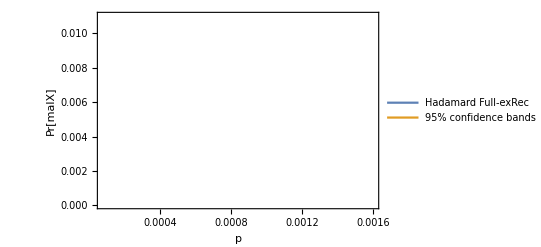

```mathematica
dataXErrFull = {{{8*10^-5,3.33*10^-5},ErrorBar[4.8596*10^-6]},{{8.5*10^-5,3.82*10^-5},ErrorBar[5.5481*10^-6]},{{9*10^-5,4.000*10^-5},ErrorBar[5.3210*10^-6]},{{9.5*10^-5,4.190*10^-5},ErrorBar[5.5200*10^-6]},{{10^-4,4.69*10^-5},ErrorBar[5.9478*10^-6]},{{2*10^-4,1.949*10^-4},ErrorBar[1.2393*10^-4]},{{3*10^-4,4.3090*10^-4},ErrorBar[1.8388*10^-5]},{{4*10^-4,7.7080*10^-4},ErrorBar[2.4592*10^-5]},{{5*10^-4,0.0012},ErrorBar[3.0853*10^-5]},
{{6*10^-4,0.0017},ErrorBar[3.6771*10^-5]},{{7*10^-4,0.0023},ErrorBar[4.2612*10^-5]},
{{8*10^-4,0.0031},ErrorBar[4.9589*10^-5]},{{9*10^-4,0.0037},ErrorBar[5.5047*10^-5]},{{10^-3,0.0046},ErrorBar[6.1231*10^-5]},
{{1.5*10^-3,0.0103},ErrorBar[9.2901*10^-5]}};
dataXErrBarOnlyFull = {4.8596*10^-6,5.5481*10^-6,5.3210*10^-6,5.5200*10^-6,5.9478*10^-6,1.2393*10^-4,1.8388*10^-5,2.4592*10^-5,3.0853*10^-5,3.6771*10^-5,4.2612*10^-5,4.9589*10^-5,5.5047*10^-5,6.1231*10^-5,9.2901*10^-5};
WeightXErr = ConstantArray[0,Length[dataXErrBarOnlyFull]];
For[i=0,i<Length[dataXErrBarOnlyFull],i++,WeightXErr[[i]]=1/(dataXErrBarOnlyFull[[i]])^2]
dataXFull = {{8*10^-5,3.33*10^-5},{8.5*10^-5,3.82*10^-5},{9*10^-5,4.000*10^-5},{9.5*10^-5,4.190*10^-5},{10^-4,4.69*10^-5},{2*10^-4,1.949*10^-4},{3*10^-4,4.3090*10^-4},{4*10^-4,7.7080*10^-4},{5*10^-4,0.0012},{6*10^-4,0.0017},{7*10^-4,0.0023},{8*10^-4,0.0031},{9*10^-4,0.0037},{10^-3,0.0046},{1.5*10^-3,0.0103}};nlmXFull=NonlinearModelFit[dataXFull,{a x^2},{a,b,c},x,Weights->{WeightXErr[[1]],WeightXErr[[2]],WeightXErr[[3]],WeightXErr[[4]],WeightXErr[[5]],WeightXErr[[6]],WeightXErr[[7]],WeightXErr[[8]],WeightXErr[[9]],WeightXErr[[10]],WeightXErr[[11]],WeightXErr[[12]],WeightXErr[[13]],WeightXErr[[14]],WeightXErr[[15]]}]
nlmXFull["EstimatedVariance"]
bands95XErr[x_]=nlmXFull["MeanPredictionBands",ConfidenceLevel->.95];
Show[ErrorListPlot[dataXFull ,PlotRange->{{8*10^-5,1.6*10^-3},{3*10^-5,0.011}}],LogLogPlot[{nlmXFull[x],bands95XErr[x],x},{x,8*10^-5,1.6*10^-3},Filling->{2->{1}},PlotLegends->{"Hadamard Full-exRec","95% confidence bands"}],Frame->True,FrameLabel->{"p","Pr[malX]"}]
```

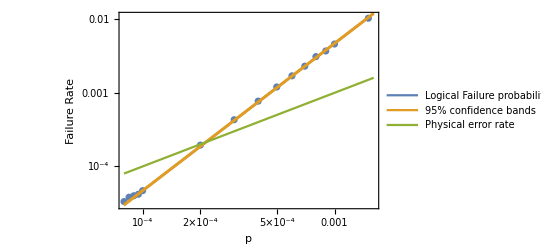

```mathematica
Show[ListLogLogPlot[dataXFull ,PlotRange->{{8*10^-5,1.6*10^-3},{3*10^-5,0.011}}],LogLogPlot[{nlmXFull[x],bands95XErr[x],x},{x,8*10^-5,1.6*10^-3},Filling->{2->{1}},PlotLegends->{"Logical Failure probability","95% confidence bands","Physical error rate"}],Frame->True,FrameLabel->{"p","Failure Rate"}]
```